/Users/miawest/Desktop/EtaPrimePhaseTransition

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {2.22029}. NIntegrate obtained -12.4313+2.06648 ⅈ and 12.4636 for the integral and error estimates.

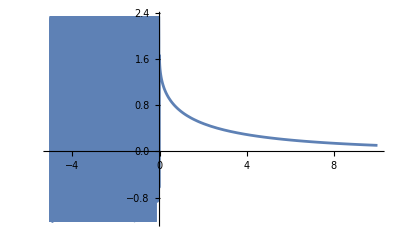

```mathematica
SetDirectory[NotebookDirectory[]]
(*Full integral fails when R^2<0 which can feasably happen*)
Ib[R2_]:=NIntegrate[x^2/(√(x^2+R2))*1/(ⅇ^(√(x^2+R2))-1),{x,0,∞}]

Plot[Re[Ib[R2]],{R2,-5,10}]
```

NIntegrate::precw: The precision of the argument function (x^2/((-1+ⅇ^(√(-0.999877+x^2))) √(-0.999877+x^2))) is less than WorkingPrecision (20.).

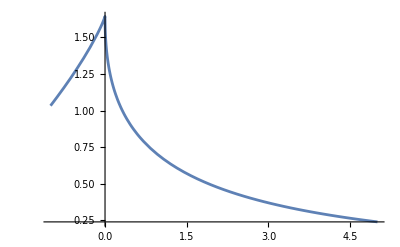

```mathematica
IB[R2_]:=NIntegrate[x^2/(√(x^2+R2))*1/(ⅇ^(√(x^2+R2))-1),{x,If[R2>0,0,√Abs[R2]+10^-10],∞},WorkingPrecision->20]+If[R2<0,NIntegrate[(-Sin[√(Abs[R2]-x^2)])/(2-2Cos[√(Abs[R2]-x^2)])*x^2/(√(Abs[R2]-x^2)),{x,0,-10^-10+√Abs[R2]}],0]

Plot[Re[IB[R2]],{R2,-1,5}]
```

NIntegrate::precw: The precision of the argument function (x^2/((-1+ⅇ^(√(-4.9998+x^2))) √(-4.9998+x^2))) is less than WorkingPrecision (20.).

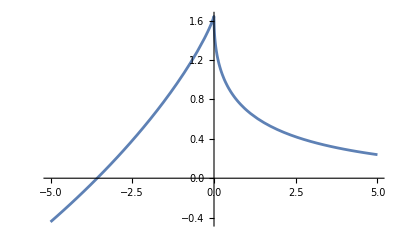

```mathematica
AbsIB[R2_]:=NIntegrate[x^2/(√(x^2+R2))*1/(ⅇ^(√(x^2+R2))-1),{x,If[R2>0,0,√Abs[R2]+10^-10],∞},WorkingPrecision->20]-If[R2<0,√((NIntegrate[(-Sin[√(Abs[R2]-x^2)])/(2-2Cos[√(Abs[R2]-x^2)])*x^2/(√(Abs[R2]-x^2)),{x,0,-10^-10+√Abs[R2]}])^2+(R2*π/8)^2),0]
Plot[AbsIB[R2],{R2,-5,5}]
```

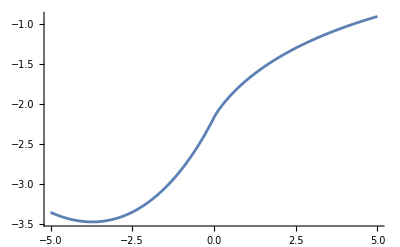

```mathematica
JB[R2_]:=NIntegrate[x^2 Log[1-Exp[-√(x^2+R2)]],{x,If[R2>0,0,√Abs[R2]+10^-20],∞}]+If[R2<0,NIntegrate[x^2 Log[2Abs[Sin[(√(Abs[R2]-x^2))/2]]],{x,0,√Abs[R2]}],0]
Plot[JB[R2],{R2,-5,5}]
```

```mathematica
(*Imaginary Part of IB vs Real*)
```

```mathematica
(*Integral of imaginary part:*)Integrate[x^2/(√(b-x^2))*1/2,{x,0,√b}]
```

ConditionalExpression[(b π)/8, Re[b]>0&&Im[b]==0]

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.4141846717152177650935193706755768621571961342333035198987556301 ⅈ}. NIntegrate obtained 0.-25.3129 ⅈ and 0.880653 for the integral and error estimates.

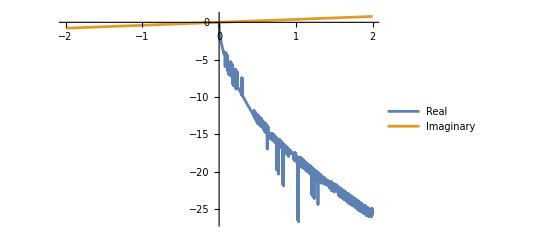

```mathematica
realIB[a_]:=NIntegrate[-x^2/(√(a-x^2))*1/2 Sin[√(a-x^2)]/(1-Cos[√(a-x^2)]),{x,0,√a}]
imaginaryIB[b_]:=(b π)/8
Plot[{realIB[c],imaginaryIB[c]},{c,-2,2},PlotLegends->{ "Real","Imaginary"}]
```

NIntegrate::zeroregion: Integration region {{0.0090396,0.0090395954397464988588906109609790134105186252351358059567527894008}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

NIntegrate::inumri: The integrand x^2/((0.0000817143-x^2)^(3/2)) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.0090395954397464988588906109609790134105186252351358059567527894008,0.0090395954397464988584372693340516108029000775389527068812295533729}}.

NIntegrate::zeroregion: Integration region {{0.0090396,0.0090395954397464988588906109609790134105186252351358059567527894008}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

NIntegrate::inumri: The integrand x^2/((0.0000817143-1. x^2)^1.5) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.0090395954397464988588906109609790134105186252351358059567527894008,0.0090395954397464988584372693340516108029000775389527068812295533729}}.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.285857249946434767634467436729686205784029606749382341015532083}. NIntegrate obtained 9.11476×10^7 and 1.83189×10^7 for the integral and error estimates.

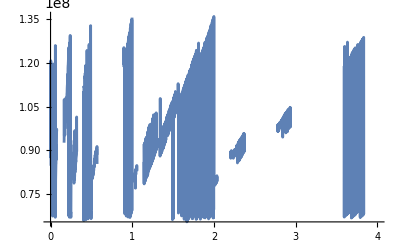

Integrate::idiv: Integral of x^2/((a-x^2)^(3/2)) does not converge on {0,√a}.

∫_0^(√a) x^2/((a-x^2)^(3/2))ⅆx

```mathematica
Plot[NIntegrate[x^2/((a-x^2)^(3/2)),{x,0,√a}],{a,0,4}]
```

```mathematica
D[x^2/(√(x^2+a))1/Exp[√(x^2+a)-1],a]
```

-(ⅇ^(1-√(a+x^2)) x^2)/(2 (a+x^2)^(3/2))-(ⅇ^(1-√(a+x^2)) x^2)/(2 (a+x^2))

```mathematica
g[a_]:=NIntegrate[Abs[D[x^2/(√(x^2+a))1/Exp[√(x^2+a)-1],a]],{x,0,√a}]
Plot[g[a],{a,-4,0}]
```

D::ivar: -3.99992 is not a valid variable.

NIntegrate::inumr: The integrand Abs[∂_-3.99992 (ⅇ^(1-√Plus[«2»]) x^2)/(√(-3.99992+x^2))] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.+0. ⅈ,0.+1.99998 ⅈ}}.

D::ivar: -3.99992 is not a valid variable.

NIntegrate::inumr: The integrand Abs[∂_-3.99992 (1. ⅇ^(1.-√Plus[«2»]) x^2)/(√(-3.99992+x^2))] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.+0. ⅈ,0.+1.99998 ⅈ}}.

D::ivar: -3.99992 is not a valid variable.

General::stop: Further output of D::ivar will be suppressed during this calculation.

NIntegrate::inumr: The integrand Abs[∂_-3.99992 (1. 2.71828^(1.-√Plus[«2»]) x^2)/(√(-3.99992+x^2))] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.+0. ⅈ,0.+1.99998 ⅈ}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

-Graphics-

```mathematica
D[x^2/(√(x^2+a))1/(Exp[√(x^2+a)]-1),a]
```

-x^2/(2 (-1+ⅇ^(√(a+x^2))) (a+x^2)^(3/2))-(ⅇ^(√(a+x^2)) x^2)/(2 (-1+ⅇ^(√(a+x^2)))^2 (a+x^2))

```mathematica
N[x^2/(2 (-1+ⅇ^(√(a+x^2))) (a+x^2)^(3/2))-(ⅇ^(√(a+x^2)) x^2)/(2 (-1+ⅇ^(√(a+x^2)))^2 (a+x^2))/.{a->1.0023063926023765,x->.05}]
```

-0.000419887

```mathematica
h[x_]:=x^2/(x^2-Abs[R2])(-1/4(1/(1-Cos[√(Abs[R2]-x^2)]))+Sin[√(Abs[R2]-x^2)]/(2(2-2Cos[√(Abs[R2]-x^2)])√(Abs[R2]-x^2)))
j[x_]:=(-1/2)x^2/((x^2-Abs[R2])(Cos[√(Abs[R2]-x^2)]-1+ⅈ Sin[√(Abs[R2]-x^2)]))((Cos[√(Abs[R2]-x^2)]+ⅈ Sin[√(Abs[R2]-x^2)])/(Cos[√(Abs[R2]-x^2)]-1+ⅈ Sin[√(Abs[R2]-x^2)])-1/(ⅈ √(Abs[R2]-x^2)))
k[x_]:=(-1/2)x^2/(x^2-Abs[R2])((Cos[√(Abs[R2]-x^2)]-1-ⅈ Sin[√(Abs[R2]-x^2)])/(2-2Cos[√(Abs[R2]-x^2)]))((1-Cos[√(Abs[R2]-x^2)]-ⅈ Sin[√(Abs[R2]-x^2)])/(2-2Cos[√(Abs[R2]-x^2)])+ⅈ/(√(Abs[R2]-x^2)))
l[x_]:=(-1/2)x^2/(x^2-Abs[R2])((-2+2Cos[√(Abs[R2]-x^2)])/((2-2Cos[√(Abs[R2]-x^2)])^2)+1/(√(Abs[R2]-x^2))(Sin[√(Abs[R2]-x^2)]+ⅈ(Cos[√(Abs[R2]-x^2)]-1))/(2-2Cos[√(Abs[R2]-x^2)]))
m[x_,R2_]:=(-1/2)x^2/(x^2-Abs[R2])(-1/(2-2Cos[√(Abs[R2]-x^2)])+1/(√(Abs[R2]-x^2))Sin[√(Abs[R2]-x^2)]/(2-2Cos[√(Abs[R2]-x^2)]))
N[h[1]/.R2->2]
N[j[1]/.R2->2]
N[k[1]/.R2->2]
N[l[1]/.R2->2]
N[m[1]/.R2->2]
```

0.0862137

-0.0862137-0.25 ⅈ

-0.0862137-0.25 ⅈ

-0.0862137-0.25 ⅈ

-0.0862137

NIntegrate::precw: The precision of the argument function (-x^2/(2 (-1+ⅇ^(√(0.0101019+Power[«2»]))) (0.0101019+x^2)^(3/2))-(ⅇ^(√(0.0101019+x^2)) x^2)/(2 (-1+ⅇ^(√(0.0101019+«1»)))^2 (0.0101019+x^2))) is less than WorkingPrecision (20.).

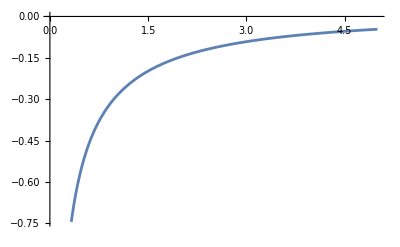

```mathematica
dIB[R2_]:=NIntegrate[-x^2/(2 (-1+ⅇ^(√(R2+x^2))) (R2+x^2)^(3/2))-(ⅇ^(√(R2+x^2)) x^2)/(2 (-1+ⅇ^(√(R2+x^2)))^2 (R2+x^2)),{x,If[R2>0,0,√Abs[R2]+10^-6],∞},WorkingPrecision->20]+If[R2<0,NIntegrate[(-1/2)x^2/(x^2-Abs[R2])(-1/(2-2Cos[√(Abs[R2]-x^2)])+1/(√(Abs[R2]-x^2))Sin[√(Abs[R2]-x^2)]/(2-2Cos[√(Abs[R2]-x^2)])),{x,0,√Abs[R2]-10^-1}],0]

Plot[Re[dIB[R2]],{R2,0.01,5}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.4141991171179312034507308039737802481511770923591621597066418647}. NIntegrate obtained -2.0981 and 0.0970917 for the integral and error estimates.

$Aborted

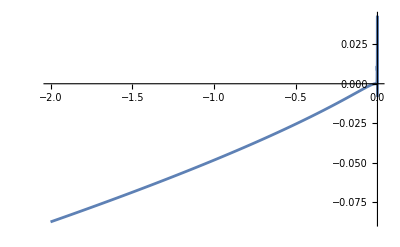

```mathematica
Plot[NIntegrate[(-1/2)x^2/(x^2-Abs[R2])(-1/(2-2Cos[√(Abs[R2]-x^2)])+1/(√(Abs[R2]-x^2))Sin[√(Abs[R2]-x^2)]/(2-2Cos[√(Abs[R2]-x^2)])),{x,0,√Abs[R2]-10^-20}],{R2,-2,0}]
```

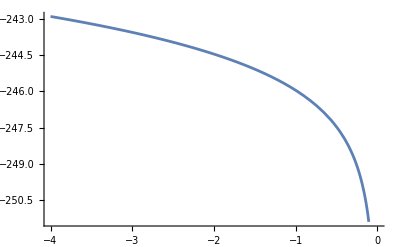

```mathematica
Plot[NIntegrate[-x^2/(2 (-1+ⅇ^(√(a+x^2))) (a+x^2)^(3/2))-(ⅇ^(√(a+x^2)) x^2)/(2 (-1+ⅇ^(√(a+x^2)))^2 (a+x^2)),{x,√Abs[a]+10^-3,∞}],{a,-4,0}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.414199117117929769517641927156059861062678613326177421327840833}. NIntegrate obtained -1.97343 and 0.00319163 for the integral and error estimates.

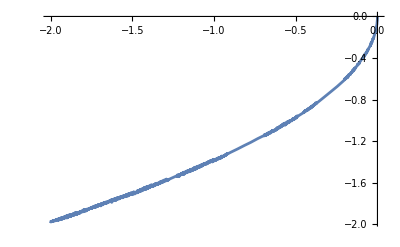

```mathematica
Plot[NIntegrate[(-1/2)x^2/(x^2-Abs[R2])(-1/(2-2Cos[√(Abs[R2]-x^2)])+1/(√(Abs[R2]-x^2))Sin[√(Abs[R2]-x^2)]/(2-2Cos[√(Abs[R2]-x^2)])),{x,0,√Abs[R2]-10^-15}],{R2,-2,0}]
```

```mathematica
NIntegrate[-x^2/(2 (-1+ⅇ^(√(x^2))) (x^2)^(3/2))-(ⅇ^(√(x^2)) x^2)/(2 (-1+ⅇ^(√(x^2)))^2 (x^2)),{x,0,∞}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.5652644542663320221104393514605137061314939823385679488488191192×10^-57}. NIntegrate obtained -2.83255×10^74 and 2.79198×10^74 for the integral and error estimates.

-2.83255×10^74

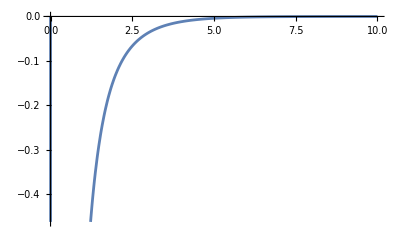

```mathematica
Plot[-x^2/(2 (-1+ⅇ^(√(a+x^2))) (a+x^2)^(3/2))-(ⅇ^(√(a+x^2)) x^2)/(2 (-1+ⅇ^(√(a+x^2)))^2 (a+x^2))/.a->.003,{x,0,10}]
```

```mathematica
(-1/2)x^2/(x^2-Abs[R2])(-1/(2-2Cos[√(Abs[R2]-x^2)])+1/(√(Abs[R2]-x^2))Sin[√(Abs[R2]-x^2)]/(2-2Cos[√(Abs[R2]-x^2)]))/.{R2->-0.001,x->0.0001}
```

-8.33369×10^-7

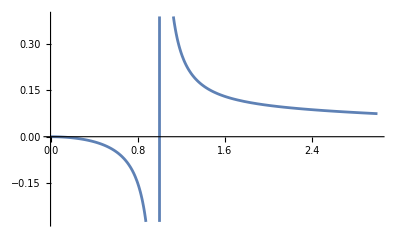

```mathematica
Plot[(-1/2)x^2/(x^2-Abs[R2])(-1/(2-2Cos[√(Abs[R2]-x^2)])+1/(√(Abs[R2]-x^2))Sin[√(Abs[R2]-x^2)]/(2-2Cos[√(Abs[R2]-x^2)]))/.R2->-1,{x,0,3}]
```

```mathematica
NIntegrate[-x^2/(2 (-1+ⅇ^(√(R2+x^2))) (R2+x^2)^(3/2))-(ⅇ^(√(R2+x^2)) x^2)/(2 (-1+ⅇ^(√(R2+x^2)))^2 (R2+x^2)),{x,If[R2>0,0,√Abs[R2]+10^-6],∞}]/.R2->1
```

NIntegrate::inumr: The integrand -x^2/(2 (-1+ⅇ^(√(R2+Power[«2»]))) (R2+x^2)^(3/2))-(ⅇ^(√(R2+x^2)) x^2)/(2 (-1+ⅇ^(√(R2+Power[«2»])))^2 (R2+x^2)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.+If[R2>0.,0.,√Abs[R2]+1.×10^-6]}}.

-0.293201

```mathematica
N[-x^2/(2 (-1+ⅇ^(√(R2+x^2))) (R2+x^2)^(3/2))-(ⅇ^(√(R2+x^2)) x^2)/(2 (-1+ⅇ^(√(R2+x^2)))^2 (R2+x^2))/.{x->0.011791212991686936,R2->0.011791212991686936}]
```

-0.950155

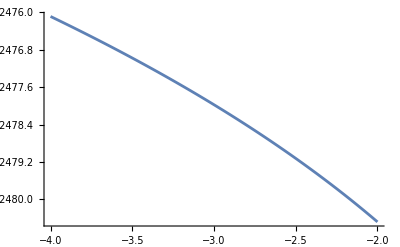

```mathematica
Plot[NIntegrate[-1/2 x^2/(x^2+R2)(1/(Exp[√(x^2+R2)]-1))*(Exp[√(x^2-Abs[R2])]/(Exp[√(x^2+R2)]-1)+1/(√(x^2+R2))),{x,√Abs[R2]+10^-4,100}],{R2,-4,-2}]
```